# Projekt Rapport

Bashar Jamal Pati, bjpati@kth.se
Mohamad Abou Helal, mohamaah@kth.se

## Uppgift

Svara på följande frågor:
1. Uppskatta världens energikonsumtion år 2050?
2. Uppskatta när olja som energikälla kan ersättas av förnybara energikällor?
3. Uppskatta om/när världens energikonsumtion är CO_2 fri?
4. Vilket förnybart energislag uppskattas vara viktigast år 2050?
5. Vad har val av modell för betydelse?
6.  Är ovanstående förutsägelser rimliga? Är förutsägelserna rimliga till 2030?
7.  Vilka felkällor finns?

#### Kol (TWh)

```mathematica
kol={{1990.,25845.88485},{1991.,25561.41954},{1992.,25478.81089},{1993.,25580.92144},{1994.,25729.64169},{1995.,25867.8533},{1996.,26516.28457},{1997.,26549.71899},{1998.,26351.79429},{1999.,26492.77461},{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}};
```

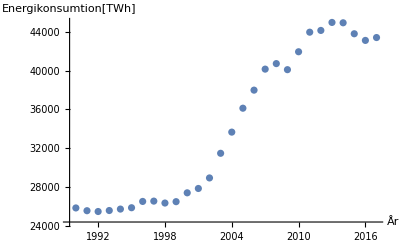

```mathematica
p=ListPlot[kol, AxesLabel->{"År", "Energikonsumtion[TWh]"}]
```

```mathematica
{x1,y1}={x,y}/.FindFit[kol,{x(t-1990)+y},{x,y},t]
```

{908.405,21826.1}

```mathematica
kol1[t_]:=x1(t-1990)+y1
```

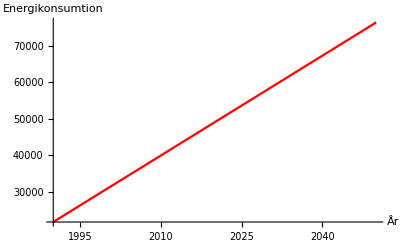

```mathematica
p1=Plot[kol1[t],{t,1990,2050}, PlotStyle->RGBColor[1, 0, 0], AxesLabel->{"År","Energikonsumtion"} ]
```

#### Olja (TWh)

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

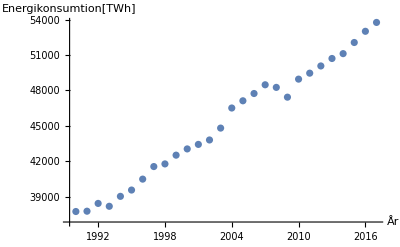

```mathematica
q=ListPlot[olja, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{x2,y2}={x,y}/.FindFit[olja,{x(t-1990)+y},{x,y},t]
```

{606.174,37053.3}

```mathematica
olja1[t_]:=x2(t-1990)+y2
```

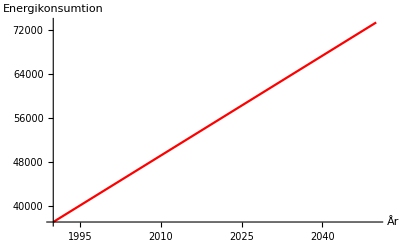

```mathematica
q1=Plot[olja1[t],{t,1990,2050}, PlotStyle->RGBColor[1, 0, 0], AxesLabel->{"År","Energikonsumtion"} ]
```

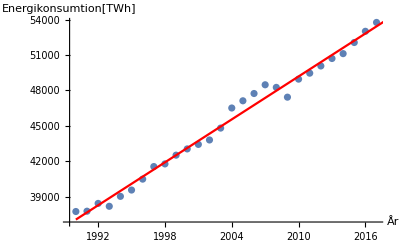

```mathematica
Show[q,q1]
```

#### Naturgas (TWh)

```mathematica
naturgas={{1990.,19486.64542},{1991.,19984.58677},{1992.,20076.92098},{1993.,20275.09431},{1994.,20405.36342},{1995.,21121.78818},{1996.,22143.41796},{1997.,22082.05319},{1998.,22485.93806},{1999.,23107.57158},{2000.,24019.89227},{2001.,24367.11133},{2002.,25108.12839},{2003.,25769.17552},{2004.,26752.16794},{2005.,27537.09099},{2006.,28347.57835},{2007.,29580.25097},{2008.,30321.37836},{2009.,29477.9263},{2010.,31759.12422},{2011.,32410.44868},{2012.,33270.53388},{2013.,33714.94785},{2014.,33986.84723},{2015.,34741.88349},{2016.,35741.82987},{2017.,36703.96587}};
```

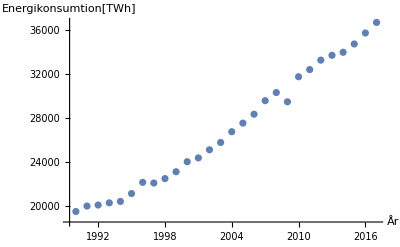

```mathematica
h1=ListPlot[naturgas,AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{x3,y3}={x,y}/.FindFit[naturgas,x(t-1990)+y,{x,y},t]
```

{665.624,17970.5}

```mathematica
naturgas1[t_]:=x3(t-1990)+y3
```

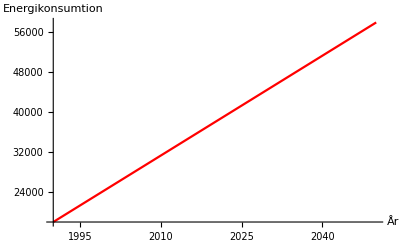

```mathematica
h2=Plot[naturgas1[t],{t,1990,2050}, PlotStyle->RGBColor[1, 0, 0], AxesLabel->{"År","Energikonsumtion"} ]
```

#### Kärnkraft (TWh)

```mathematica
karnkraft={{1990.,2000.642591},{1991.,2096.356868},{1992.,2112.277946},{1993.,2185.016841},{1994.,2226.050783},{1995.,2322.592422},{1996.,2407.002623},{1997.,2390.480054},{1998.,2431.571247},{1999.,2524.546817},{2000.,2580.976669},{2001.,2653.821898},{2002.,2696.204132},{2003.,2641.599256},{2004.,2757.124087},{2005.,2769.046942},{2006.,2803.605088},{2007.,2746.479825},{2008.,2737.860822},{2009.,2699.245242},{2010.,2767.507814},{2011.,2651.771616},{2012.,2472.44864},{2013.,2491.705601},{2014.,2541.027341},{2015.,2575.664304},{2016.,2612.83283},{2017.,2635.561104}};
```

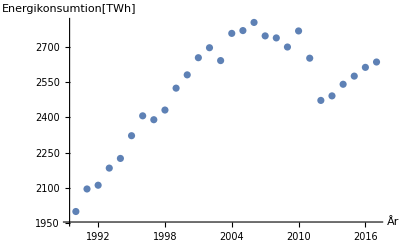

```mathematica
f=ListPlot[karnkraft,AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
karnkraft0=Take[karnkraft,-17]
```

{{2001.,2653.82},{2002.,2696.2},{2003.,2641.6},{2004.,2757.12},{2005.,2769.05},{2006.,2803.61},{2007.,2746.48},{2008.,2737.86},{2009.,2699.25},{2010.,2767.51},{2011.,2651.77},{2012.,2472.45},{2013.,2491.71},{2014.,2541.03},{2015.,2575.66},{2016.,2612.83},{2017.,2635.56}}

```mathematica
{x4,y4}={x,y}/.FindFit[karnkraft0,x(t-1990)+y,{x,y},t]
```

{-10.9519,2870.06}

```mathematica
karnkraft1[t_]:=x4(t-1990)+y4
```

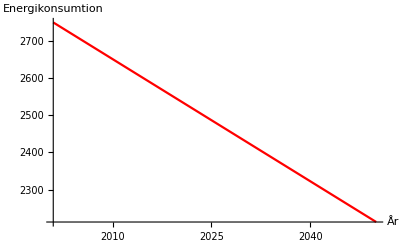

```mathematica
f1=Plot[karnkraft1[t],{t,2001,2050}, PlotStyle->RGBColor[1, 0, 0], AxesLabel->{"År","Energikonsumtion"} ]
```

#### Bio-bränslen (TWh)

```mathematica
biobransle={{1990.,11111.11111},{1991.,11242.7549},{1992.,11375.95839},{1993.,11510.74008},{1994.,11647.11865},{1995.,11785.11302},{1996.,11924.74234},{1997.,12066.02598},{1998.,12208.98355},{1999.,12414.05573},{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.70237},{2004.,12159.75217},{2005.,12076.14729},{2006.,11993.11724},{2007.,11910.65806},{2008.,11828.76583},{2009.,11747.43666},{2010.,11666.66667},{2011.,11553.3766},{2012.,11441.18663},{2013.,11330.0861},{2014.,11220.06442},{2015.,11111.11111},{2016.,11003.2158},{2017.,10895.32049}};
```

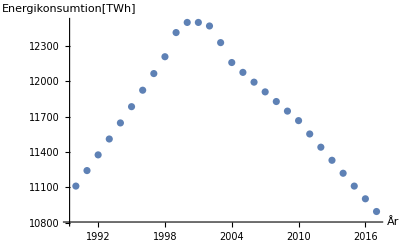

```mathematica
k=ListPlot[biobransle, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
biobransle1=Take[biobransle,-17]
```

{{2001.,12500.},{2002.,12470.},{2003.,12328.7},{2004.,12159.8},{2005.,12076.1},{2006.,11993.1},{2007.,11910.7},{2008.,11828.8},{2009.,11747.4},{2010.,11666.7},{2011.,11553.4},{2012.,11441.2},{2013.,11330.1},{2014.,11220.1},{2015.,11111.1},{2016.,11003.2},{2017.,10895.3}}

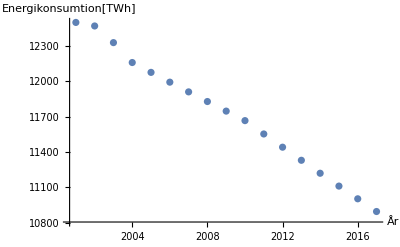

```mathematica
k1=ListPlot[biobransle1, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{x5,y5}={x,y}/.FindFit[biobransle1,{x(t-2001)+y},{x,y},t]
```

{-99.5726,12516.3}

```mathematica
biobransle2[t_]:=x5(t-2001)+y5
```

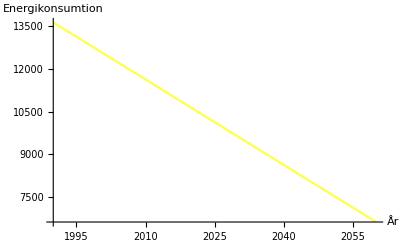

```mathematica
k2=Plot[x5(t-2001)+y5,{t,1990,2060},PlotStyle->RGBColor[1, 1, 0.282353], AxesLabel->{"År","Energikonsumtion"}]
```

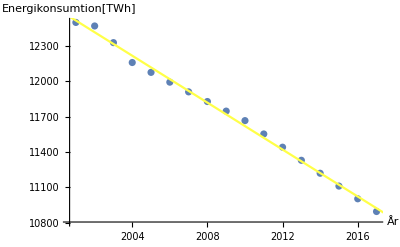

```mathematica
Show [k1,k2]
```

#### Andra Förnybara Energikällor (TWh)

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

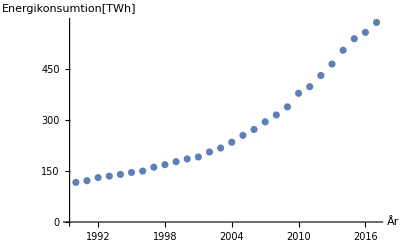

```mathematica
m1=ListPlot[andrafornybara, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{a1,b1}={a,b}/.FindFit[andrafornybara,{a Exp[b(t-1990)]},{a,b},t]
```

{97.3992,0.0670767}

```mathematica
andrafornybara1[t_]:=a1 Exp[b1(t-1990)]
```

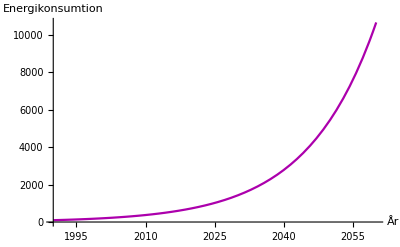

```mathematica
m2=Plot[andrafornybara1[t],{t,1990,2060},PlotStyle->RGBColor[0.67451, 0, 0.67451], AxesLabel->{"År","Energikonsumtion"}]
```

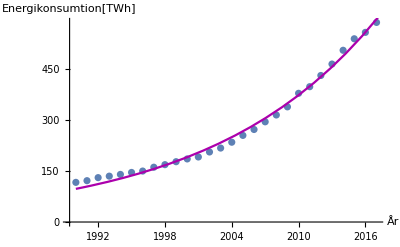

```mathematica
Show[m1,m2]
```

#### Vattenkraft (TWh)

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

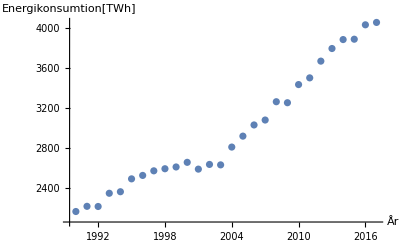

```mathematica
n1=ListPlot[vatten, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{x6,y6}={x,y}/.FindFit[vatten,{x(t-1990)+y},{x,y},t]
```

{71.3453,2008.72}

```mathematica
vatten1[t_]:=x6(t-1990)+y6
```

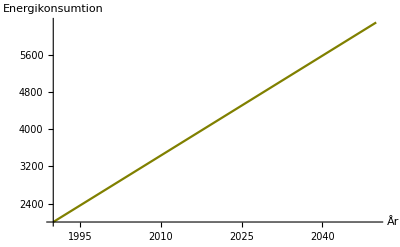

```mathematica
n2=Plot[vatten1[t],{t,1990,2050},PlotStyle-> {RGBColor[0.501961, 0.501961, 0]},AxesLabel-> {"År","Energikonsumtion"} ]
```

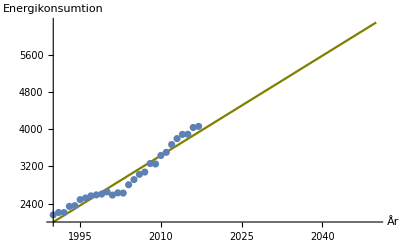

```mathematica
Show[n2,n1]
```

#### Vindkraft (TWh)

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

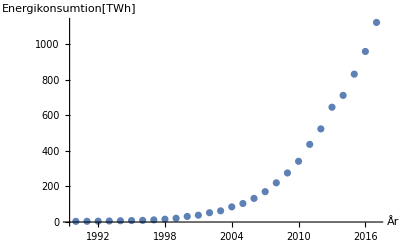

```mathematica
c1=ListPlot[vind, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{a2,b2}={a,b}/.FindFit[vind,{a Exp[b(t-1990)]},{a,b},t]
```

{9.25548,0.179304}

```mathematica
vind1[t_]:=a2 Exp[b2(t-1990)]
```

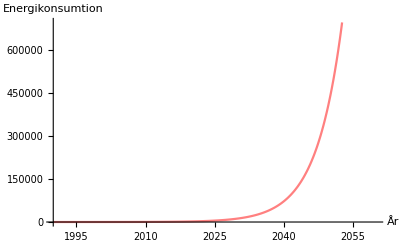

```mathematica
c2=Plot[vind1[t],{t,1990,2060},PlotStyle->{ RGBColor[1, 0.501961, 0.501961]},AxesLabel-> {"År","Energikonsumtion"}]
```

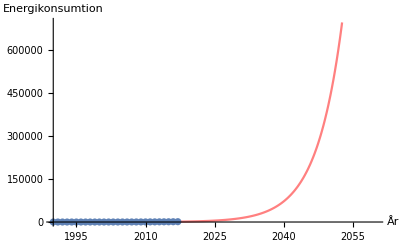

```mathematica
Show[c2,c1]
```

#### Solenergi (TWh)

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

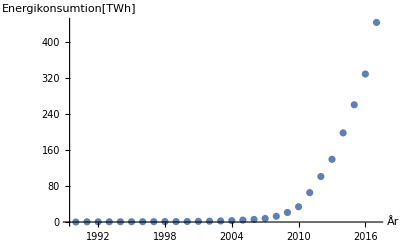

```mathematica
o1=ListPlot[sol, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{a3,b3}={a,b}/.FindFit[sol,{a Exp[b(t-1990)]},{a,b},t]
```

{0.104136,0.310299}

```mathematica
sol1[t_]:=a3 Exp[b3(t-1990)]
```

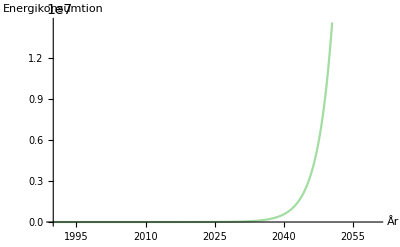

```mathematica
o2=Plot[sol1[t],{t,1990,2060},PlotStyle->{RGBColor[0.635294, 0.866667, 0.635294]},AxesLabel->{"År","Energikonsumtion"}]
```

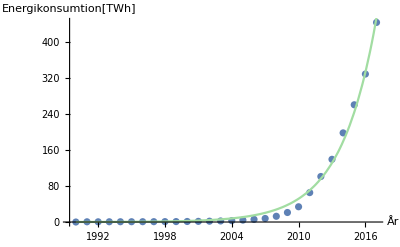

```mathematica
Show[o1,o2]
```

#### Världens total energikonsumtion (TWh)

```mathematica
totalt={{1990.,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}};
```

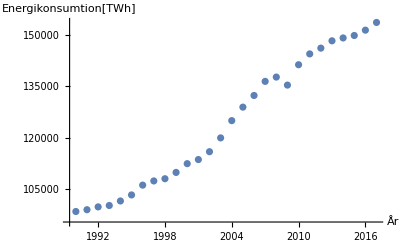

```mathematica
z=ListPlot[totalt, AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
{x7,y7}={x,y}/.FindFit[totalt,x(t-1990)+y,{x,y},t]
```

{2314.87,92855.}

```mathematica
etotal[t_]:=x7(t-1990)+y7
```

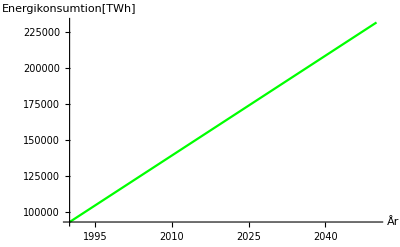

```mathematica
z1=Plot[etotal[t],{t,1990,2050}, PlotStyle->RGBColor[0, 1, 0],AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

## Uppgifter

### Världens energikonsumtion

1. Uppskatta världens energikonsumtion år 2050?

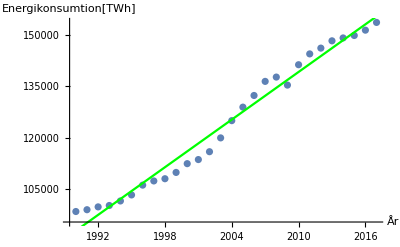

```mathematica
Show[z,z1]
```

```mathematica
etotal[2050]
```

231747.

- År 2050 kommer att världens energikonsumtion vara ungefär 232 kTWh.

### Olja som förnybara engergiköllor.

2. Uppskatta när olja som energikälla kan ersättas av förnybara energikällor?

```mathematica
Allfornybara1[t_]:=biobransle2[t]+andrafornybara1[t]+vatten1[t]+vind1[t]+sol1[t]
```

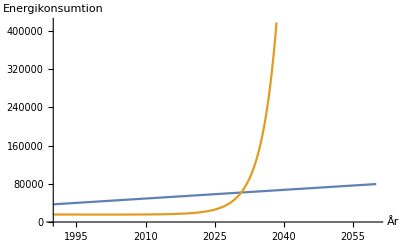

```mathematica
Plot[{olja1[t],Allfornybara1[t]},{t,1990,2060},AxesLabel->{"År","Energikonsumtion"}]
```

```mathematica
t/.FindRoot[Allfornybara1[t]==olja1[t],{t,2040}]
```

2030.72

- Som energikälla kommer oljan ersättas av förnybara ungefär år 2031

### Fri av CO_2

3. Uppskatta om / när världens energiskonsumtion är CO_2 fri?

```mathematica
co2fri1[t_]:=Allfornybara1[t]+karnkraft1[t]
```

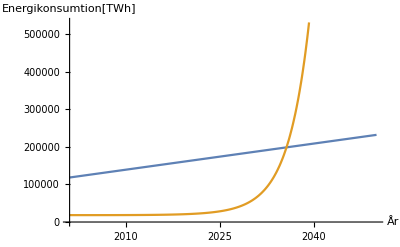

```mathematica
Plot[{etotal[t],co2fri1[t]},{t,2001,2050},AxesLabel->{"År","Energikonsumtion[TWh]"}]
```

```mathematica
t/.FindRoot[co2fri1[t]==etotal[t],{t,2025}]
```

2035.63

- Världens energikonsumtion kommer att vara fri av CO_2 år 2036.

### Viktigast energislag

Vilket förnybart energislag uppskattas vara viktigast år 2050?

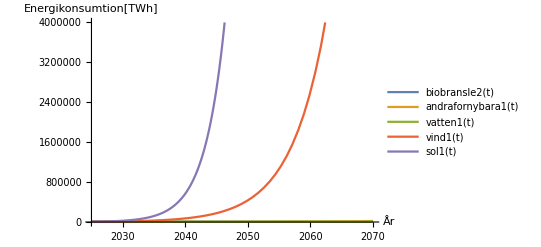

```mathematica
Plot[{biobransle2[t],andrafornybara1[t],vatten1[t],vind1[t],sol1[t]},{t,2025,2070},PlotRange->{{2025,2070},{0,4×10^6}}, AxesLabel->{"År","Energikonsumtion[TWh]"}, PlotLegends->"Expressions"]
```

```mathematica
biobransle2[2050]
```

7637.27

```mathematica
andrafornybara1[2050]
```

5450.26

```mathematica
vatten1[2050]
```

6289.44

```mathematica
vind1[2050]
```

435144.

```mathematica
sol1[2050]
```

1.26844×10^7

- År 2050 kommer solen vara den viktigaste energikälla i världen. Detta ser vi med värdet på solenskonsumtion som är 12.7MTWh.

### Modellens betydelse.

Vad har val av modell för betydelse?

- För att kunna skissera en funktion i ett koordinatsystem behöver funktionen en speciell modell som till exempel linjärfunktion. För att anpassa dessutom dessa punkter med den funktionen så spelar stor roll vad har funktionen för typ(modell). Det kan således vara svårt om man ska skissera en exponentialfunktion med en linjärfunktion eftersom punkterna kommer inte stämma överens med själva linje.

### Rimlighet av förutsägelser.

Är ovanstående förutsägelser rimliga? Är förutsägelserna rimliga till 2030?

Från det vi lever idag kan dessa förutsägelser vara rimliga efterson världen håller på att förbättra när det gäller hållbarhet. Exempelvis har solceller varit mer populära under de senaste åren och det används mer, detta gör att sol energi har ökat och kan räknas som viktigast energislag.

### Felkällor

Vilka felkällor finns?

Avrundning av decimaler kan möjligtvis vara en av de felkällor som vi kan möta. Eftersom siffror som vi räknat har avrundat till ett antal decimaler så svaret kan ha mindre säkerthet och tydlighet. Dessutom vet vi inte om hur mycket av våra källor kan man lita på för det finns inga referenser som gör att källor bli äkta.